```mathematica
coefs={-0.1628144585364618,1.0938240550863623,-1.7893*^-12,-0.0388330290615209,4.2068*^-12,0.0058637635731647,-3.8354*^-12,-0.0012449499435649,1.3109*^-12,0.0003035681797625,1.9562*^-12,-0.0000795509260935,-8.6277*^-12,0.0000218142857332,9.5162*^-12,-6.1819173587*^-6,6.307*^-13,1.7974479634*^-6,-1.43203*^-11,-5.334745204*^-7,1.42301*^-11,1.609769975*^-7,-4.9777*^-12,-4.92412545*^-8,-2.09951*^-11,1.52481128*^-8,2.77066*^-11,-4.7711989*^-9,-1.13903*^-11,1.4635423*^-9,-1.13087*^-11,-3.706093*^-10};
```

```mathematica
F[x_]:=Sin[x]
min=-2Pi;
max=2Pi;
```

```mathematica
FourierApprox[coefs_][x_]:=Sum[coefs[[i+1]]*Sin[i*x], {i, 0,Length[coefs]-1}]
TaylorApprox[coefs_][x_]:=Sum[coefs[[i+1]]*x^i/Factorial[i], {i, 0, Length[coefs]-1}]
IntegralLoss[f_]:=NIntegrate[(F[x]-f[f[x]])^2, {x, min, max}]
```

```mathematica
approx=FourierApprox[coefs];
```

```mathematica
IntegralLoss[approx]
```

1.36716×10^-19

```mathematica
Iconize[approx[x]]
```

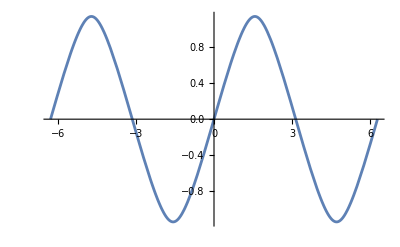

```mathematica
Plot[ approx[x], {x, min, max}]
```

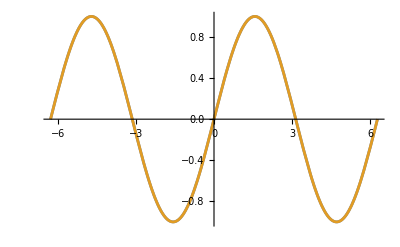

```mathematica
Plot[{F[x], approx[approx[x]]}, {x, min, max}]
```

```mathematica
approx[x]
```

0.+1.09382 Sin[x]-1.7893×10^-12 Sin[2 x]-0.038833 Sin[3 x]+4.2068×10^-12 Sin[4 x]+0.00586376 Sin[5 x]-3.8354×10^-12 Sin[6 x]-0.00124495 Sin[7 x]+1.3109×10^-12 Sin[8 x]+0.000303568 Sin[9 x]+1.9562×10^-12 Sin[10 x]-0.0000795509 Sin[11 x]-8.6277×10^-12 Sin[12 x]+0.0000218143 Sin[13 x]+9.5162×10^-12 Sin[14 x]-6.18192×10^-6 Sin[15 x]+6.307×10^-13 Sin[16 x]+1.79745×10^-6 Sin[17 x]-1.43203×10^-11 Sin[18 x]-5.33475×10^-7 Sin[19 x]+1.42301×10^-11 Sin[20 x]+1.60977×10^-7 Sin[21 x]-4.9777×10^-12 Sin[22 x]-4.92413×10^-8 Sin[23 x]-2.09951×10^-11 Sin[24 x]+1.52481×10^-8 Sin[25 x]+2.77066×10^-11 Sin[26 x]-4.7712×10^-9 Sin[27 x]-1.13903×10^-11 Sin[28 x]+1.46354×10^-9 Sin[29 x]-1.13087×10^-11 Sin[30 x]-3.70609×10^-10 Sin[31 x]

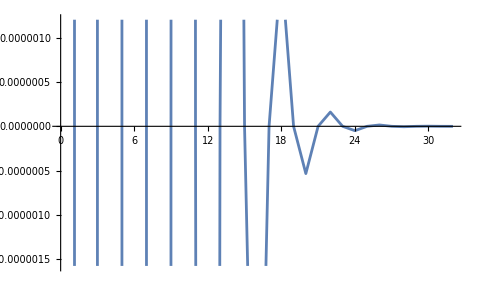

```mathematica
ListLinePlot[coefs]
```